```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/benchmarks/float_sort_benchmarks.csv"];
data=Take[data,{11,data//Length}];
headers=Partition[data[[1]],11];
cols=data[[1]];
data=Take[data,{2,data//Length}];
```

```mathematica
benchmarks={"bitonic_2n_float_sort_bench", "bitonic_8n_float_sort_bench","bitonic_float_sort_bench", "std_float_sort_bench", "hybrid_8n_float_sort_bench", "improved_bitonic_float_sort_bench"};
cols
```

{bitonic_2n_float_sort_bench/8,879424,779.889,774.914,ns,,,,,,8}

```mathematica
GetBenchData[name_]:=Block [{tab},
tab=Table[If[(StringMatchQ[data[[i,1]], name]  && Length[data[[i]]]>5)≠0,data[[i]], ""],{i,1,data//Length}];
tab=DeleteCases[tab, ""];
Return [tab];
];
```

```mathematica
data;
```

```mathematica
data1=GetBenchData[benchmarks[[1]]];
data1=Take[data1, {1, (data1//Length)-2}];
timing1=data1[[All,4]];
NumToSort1=data1[[All,11]];
```

Part::partw: Part 4 of If[False≠0,data⟦i⟧,] does not exist.

Part::partw: Part 11 of If[False≠0,data⟦i⟧,] does not exist.

```mathematica
data2=GetBenchData[benchmarks[[2]]];
data2=Take[data2, {1, (data2//Length)-2}];
timing2=data2[[All,4]];
NumToSort2=data2[[All,11]];
```

```mathematica
data3=GetBenchData[benchmarks[[3]]];
data3=Take[data3, {1, (data3//Length)-2}];
timing3=data3[[All,4]];
NumToSort3=data3[[All,11]];
```

```mathematica
data4=GetBenchData[benchmarks[[4]]];
data4=Take[data4, {1, (data4//Length)-2}];
timing4=data4[[All,4]];
NumToSort4=data4[[All,11]];
```

```mathematica
data5=GetBenchData[benchmarks[[5]]];
data5=Take[data5, {1, (data5//Length)-2}];
timing5=data5[[All,4]];
NumToSort5=data5[[All,11]];
```

```mathematica
data6=GetBenchData[benchmarks[[6]]];
data6=Take[data6, {1, (data6//Length)-2}];
timing6=data6[[All,4]];
NumToSort6=data6[[All,11]];
```

```mathematica
p1=Transpose[{NumToSort1,timing1}];
p2=Transpose[{NumToSort2,timing2}];
p3=SortBy[Transpose[{NumToSort3,timing3}], First];
p4=SortBy[Transpose[{NumToSort4,timing4}], First];
p5=SortBy[Transpose[{NumToSort5,timing5}], First];
p6=SortBy[Transpose[{NumToSort6,timing6}], First];
```

```mathematica
data3
```

{{bitonic_float_sort_bench/10,787655,882.83,878.268,ns,,,,,,10},{bitonic_float_sort_bench/20,464960,1814.6,1678.21,ns,,,,,,20},{bitonic_float_sort_bench/40,341168,1887.89,1878.38,ns,,,,,,40},{bitonic_float_sort_bench/50,351914,1922.53,1928.62,ns,,,,,,50},{bitonic_float_sort_bench/80,369711,1886.62,1886.93,ns,,,,,,80},{bitonic_float_sort_bench/100,249981,2987.79,2994.54,ns,,,,,,100},{bitonic_float_sort_bench/200,203708,3449.83,3446.92,ns,,,,,,200},{bitonic_float_sort_bench/400,102352,6687.86,6680.12,ns,,,,,,400},{bitonic_float_sort_bench/800,49386,14628,14629,ns,,,,,,800},{bitonic_float_sort_bench/1600,21142,31764.8,31745,ns,,,,,,1600},{bitonic_float_sort_bench/3200,9478,72913.6,72797.6,ns,,,,,,3200},{bitonic_float_sort_bench/5000,5505,127414,127281,ns,,,,,,5000},{bitonic_float_sort_bench/7500,2521,282439,282053,ns,,,,,,7500},{bitonic_float_sort_bench/10000,2482,280402,279975,ns,,,,,,10000},{bitonic_float_sort_bench/12000,2075,337613,337192,ns,,,,,,12000},{bitonic_float_sort_bench/15000,1649,427166,427689,ns,,,,,,15000},{bitonic_float_sort_bench/17000,1302,533903,534396,ns,,,,,,17000},{bitonic_float_sort_bench/20000,1073,635982,636620,ns,,,,,,20000},{bitonic_float_sort_bench/25000,867,802364,802772,ns,,,,,,25000},{bitonic_float_sort_bench/27000,805,872881,872865,ns,,,,,,27000},{bitonic_float_sort_bench/30000,727,964895,965107,ns,,,,,,30000},{bitonic_float_sort_bench/35000,576,1.22944×10^6,1.22975×10^6,ns,,,,,,35000},{bitonic_float_sort_bench/40000,503,1.38151×10^6,1.38186×10^6,ns,,,,,,40000},{bitonic_float_sort_bench/50000,404,1.75582×10^6,1.75573×10^6,ns,,,,,,50000},{bitonic_float_sort_bench/70000,100,5.13918×10^6,5.05484×10^6,ns,,,,,,70000},{bitonic_float_sort_bench/100000,95,5.64884×10^6,5.47875×10^6,ns,,,,,,100000},{bitonic_float_sort_bench/120000,93,7.17778×10^6,7.01044×10^6,ns,,,,,,120000},{bitonic_float_sort_bench/150000,79,8.21755×10^6,8.18488×10^6,ns,,,,,,150000},{bitonic_float_sort_bench/200000,60,1.17418×10^7,1.10568×10^7,ns,,,,,,200000},{bitonic_float_sort_bench/400000,27,4.19815×10^7,3.63002×10^7,ns,,,,,,400000},{bitonic_float_sort_bench/600000,12,4.7027×10^7,4.42893×10^7,ns,,,,,,600000},{bitonic_float_sort_bench/800000,12,4.36809×10^7,4.36122×10^7,ns,,,,,,800000},{bitonic_float_sort_bench/1000000,12,6.58236×10^7,6.57586×10^7,ns,,,,,,1.×10^6},{bitonic_float_sort_bench/1200000,8,8.75445×10^7,8.75253×10^7,ns,,,,,,1.2×10^6},{bitonic_float_sort_bench/1500000,4,1.44844×10^8,1.42476×10^8,ns,,,,,,1.5×10^6},{bitonic_float_sort_bench/1800000,3,1.79985×10^8,1.7939×10^8,ns,,,,,,1.8×10^6},{bitonic_float_sort_bench/2000000,5,1.65624×10^8,1.65095×10^8,ns,,,,,,2.×10^6},{bitonic_float_sort_bench/2500000,3,2.33173×10^8,2.33158×10^8,ns,,,,,,2.5×10^6},{bitonic_float_sort_bench/3000000,3,2.01497×10^8,2.01506×10^8,ns,,,,,,3.×10^6},{bitonic_float_sort_bench/5000000,2,3.61098×10^8,3.61084×10^8,ns,,,,,,5.×10^6},{bitonic_float_sort_bench/7000000,1,5.12603×10^8,5.12618×10^8,ns,,,,,,7.×10^6},{bitonic_float_sort_bench/10000000,1,8.37153×10^8,8.37181×10^8,ns,,,,,,1.×10^7},{improved_bitonic_float_sort_bench/10,863208,786.389,787.125,ns,,,,,,10},{improved_bitonic_float_sort_bench/20,660715,1116.14,1120.53,ns,,,,,,20},{improved_bitonic_float_sort_bench/40,535990,1260.55,1263.25,ns,,,,,,40},{improved_bitonic_float_sort_bench/50,442846,1604,1608.24,ns,,,,,,50},{improved_bitonic_float_sort_bench/80,374192,1807.44,1811.73,ns,,,,,,80},{improved_bitonic_float_sort_bench/100,264085,2705.85,2714.05,ns,,,,,,100},{improved_bitonic_float_sort_bench/200,173606,4520.76,4527.72,ns,,,,,,200},{improved_bitonic_float_sort_bench/400,85081,7859.6,7873.7,ns,,,,,,400},{improved_bitonic_float_sort_bench/800,42760,16082.4,16109.7,ns,,,,,,800},{improved_bitonic_float_sort_bench/1600,19351,37924.5,37996.9,ns,,,,,,1600},{improved_bitonic_float_sort_bench/3200,8042,82739.9,82893.5,ns,,,,,,3200},{improved_bitonic_float_sort_bench/5000,4907,144456,144745,ns,,,,,,5000},{improved_bitonic_float_sort_bench/7500,2248,303856,304384,ns,,,,,,7500},{improved_bitonic_float_sort_bench/10000,2204,319133,319516,ns,,,,,,10000},{improved_bitonic_float_sort_bench/12000,1861,381945,382361,ns,,,,,,12000},{improved_bitonic_float_sort_bench/15000,1451,475523,476119,ns,,,,,,15000},{improved_bitonic_float_sort_bench/17000,1121,638945,639484,ns,,,,,,17000},{improved_bitonic_float_sort_bench/20000,985,725652,726058,ns,,,,,,20000},{improved_bitonic_float_sort_bench/25000,696,937616,932104,ns,,,,,,25000},{improved_bitonic_float_sort_bench/27000,698,957926,958073,ns,,,,,,27000},{improved_bitonic_float_sort_bench/30000,647,1.04843×10^6,1.0488×10^6,ns,,,,,,30000},{improved_bitonic_float_sort_bench/35000,515,1.3698×10^6,1.36975×10^6,ns,,,,,,35000},{improved_bitonic_float_sort_bench/40000,432,1.56358×10^6,1.56385×10^6,ns,,,,,,40000},{improved_bitonic_float_sort_bench/50000,361,1.94212×10^6,1.94179×10^6,ns,,,,,,50000},{improved_bitonic_float_sort_bench/70000,234,3.00712×10^6,3.00754×10^6,ns,,,,,,70000},{improved_bitonic_float_sort_bench/100000,165,4.30698×10^6,4.3069×10^6,ns,,,,,,100000},{improved_bitonic_float_sort_bench/120000,136,5.09075×10^6,5.08977×10^6,ns,,,,,,120000},{improved_bitonic_float_sort_bench/150000,98,7.11431×10^6,7.11484×10^6,ns,,,,,,150000},{improved_bitonic_float_sort_bench/200000,74,9.49584×10^6,9.49319×10^6,ns,,,,,,200000},{improved_bitonic_float_sort_bench/400000,34,2.09094×10^7,2.09111×10^7,ns,,,,,,400000},{improved_bitonic_float_sort_bench/600000,20,3.42373×10^7,3.42336×10^7,ns,,,,,,600000},{improved_bitonic_float_sort_bench/800000,15,4.66577×10^7,4.66459×10^7,ns,,,,,,800000},{improved_bitonic_float_sort_bench/1000000,12,5.84019×10^7,5.84047×10^7,ns,,,,,,1.×10^6},{improved_bitonic_float_sort_bench/1200000,9,7.59311×10^7,7.59321×10^7,ns,,,,,,1.2×10^6},{improved_bitonic_float_sort_bench/1500000,7,9.73341×10^7,9.73386×10^7,ns,,,,,,1.5×10^6},{improved_bitonic_float_sort_bench/1800000,6,1.16799×10^8,1.16803×10^8,ns,,,,,,1.8×10^6},{improved_bitonic_float_sort_bench/2000000,5,1.33422×10^8,1.33428×10^8,ns,,,,,,2.×10^6},{improved_bitonic_float_sort_bench/2500000,4,1.77558×10^8,1.77481×10^8,ns,,,,,,2.5×10^6},{improved_bitonic_float_sort_bench/3000000,3,2.12666×10^8,2.126×10^8,ns,,,,,,3.×10^6},{improved_bitonic_float_sort_bench/5000000,2,4.03689×10^8,4.03703×10^8,ns,,,,,,5.×10^6}}

```mathematica
color=ColorData[10,"ColorList"];
benchmarks
LegendFontSize=20;
legenda=
PointLegend[{
{color[[1]],AbsolutePointSize[8]},
{color[[2]],AbsolutePointSize[8]},
{color[[3]],AbsolutePointSize[8]},
{color[[4]], AbsolutePointSize[8]},
{color[[5]], AbsolutePointSize[8]},
{color[[6]], AbsolutePointSize[8]},
Directive[color[[9]], AbsolutePointSize[8]]},
{Style["bitonic 2^n sort", LegendFontSize], Style["bitonic 8n sort", LegendFontSize], Style["bitonic arbitrary n sort", LegendFontSize], 
Style["std sort", LegendFontSize], Style["hybrid 8n sort", LegendFontSize],  Style["bitonic sort ver2", LegendFontSize]},
LegendLabel->"", LegendLayout->{"Row",6}];
```

{bitonic_2n_float_sort_bench,bitonic_8n_float_sort_bench,bitonic_float_sort_bench,std_float_sort_bench,hybrid_8n_float_sort_bench,improved_bitonic_float_sort_bench}

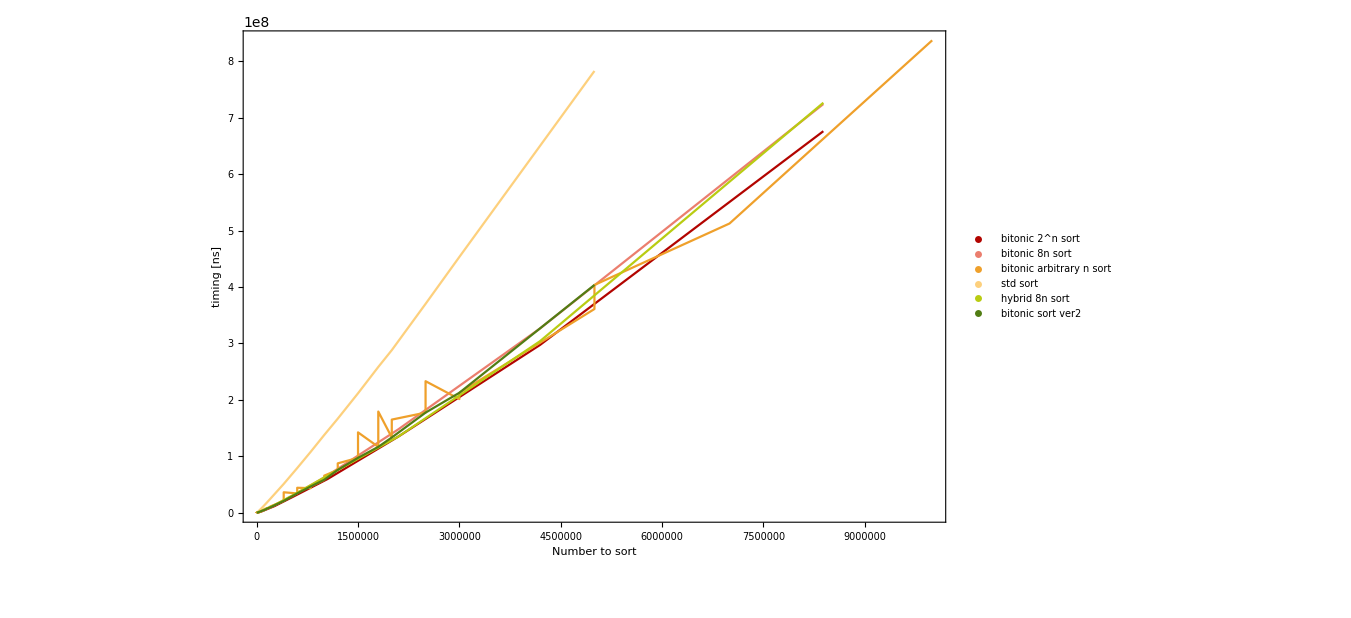

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4, p5, p6
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {1*10^7, 4*10^9}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True, 
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->All,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

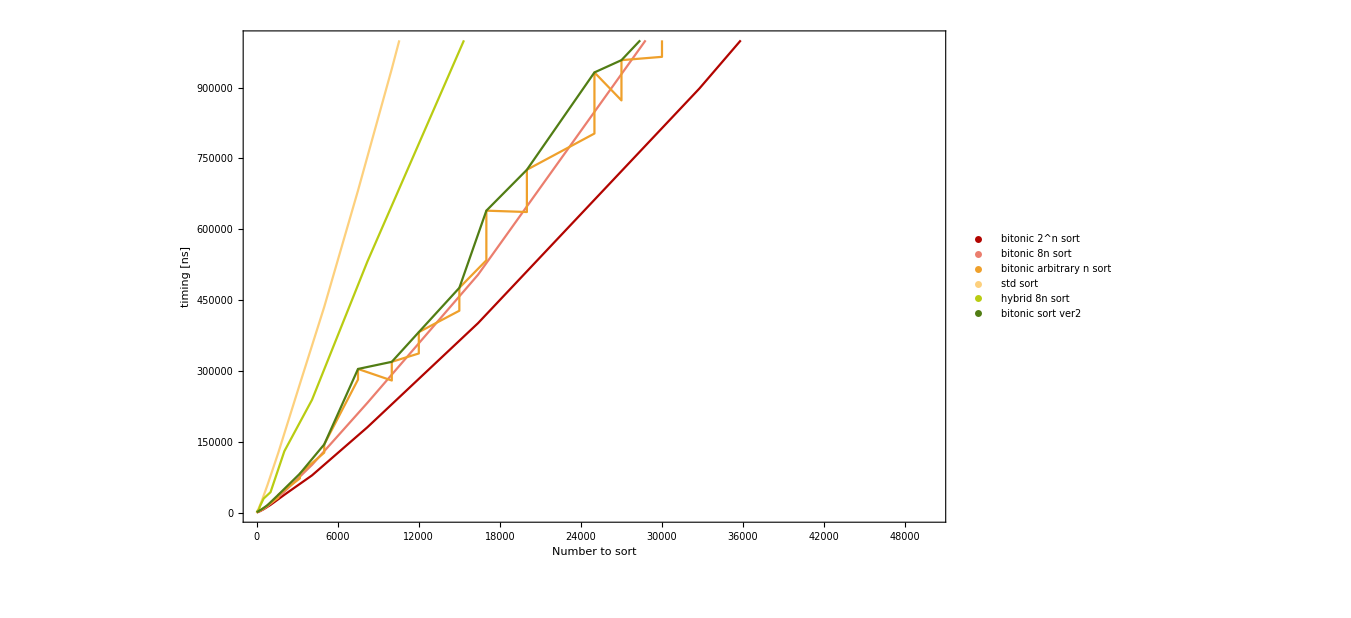

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4, p5, p6
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {4*10^4, 2.2*10^5}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0, 50000},{0, 10 ^6}},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

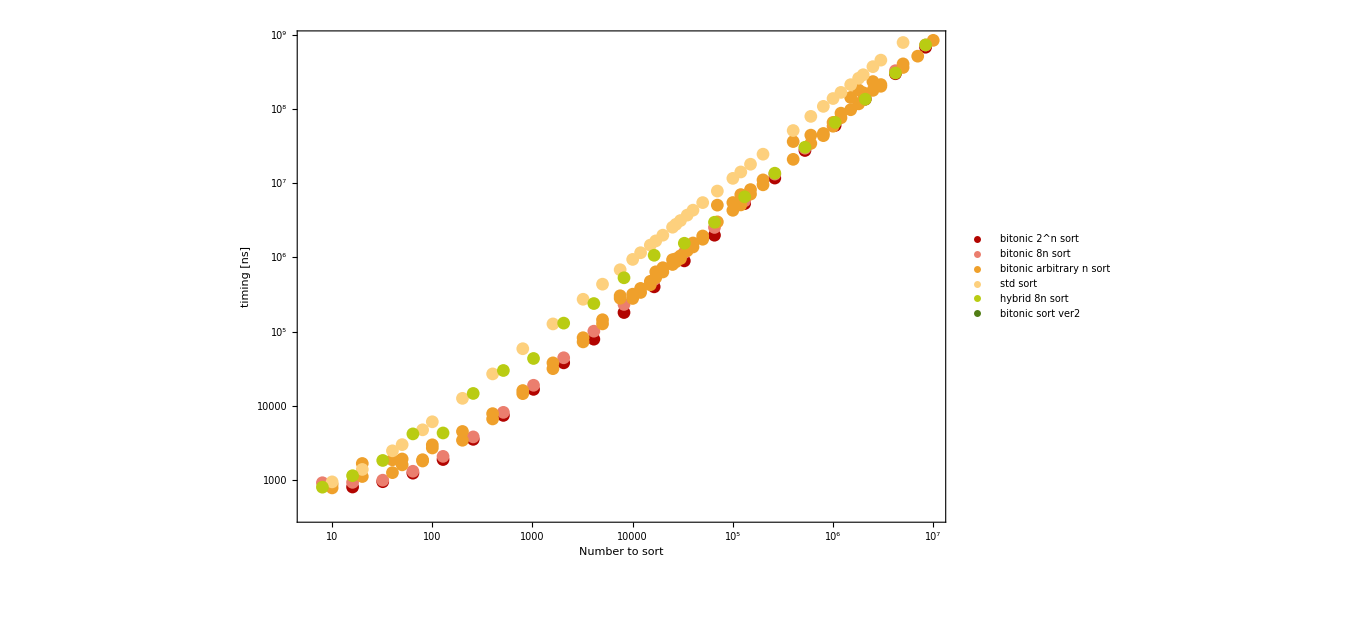

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLogLogPlot[{
p1,p2,p3,p4, p5
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]]},
Epilog->Inset[legenda, {1*10^6, 2*10^8}],
AxesOrigin->{-100, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->Automatic,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

```mathematica
NonlinearModelFit[Take[p1, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p2, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p3, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p4, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
```

FittedModel[9.25275 x+1.00715×10^-6 x^2+0.247475 x Log[x]^2]

FittedModel[-3.60289 x+2.21632×10^-7 x^2+0.346565 x Log[x]^2]

FittedModel[229.933 x+5.27605×10^-6 x^2-0.767553 x Log[x]^2]

FittedModel[-19.2464 x-3.45515×10^-6 x^2+0.811623 x Log[x]^2]

```mathematica
(*speedup calculation in comparison to std*)

speedup1=Table[{p3[[i,1]],p4[[i,2]]/p3[[i,2]]},{i,1,p3//Length}]//N;
```

Part::partw: Part 41 of {{10,948.817},{20,1395.01},{40,2485.5},{50,3010.58},{80,4766.77},{100,6115.91},{200,12647},{400,26985.6},{800,58924},{1600,127092},{3200,272939},{5000,435818},{7500,682165},{10000,939617},{12000,1.15614×10^6},{15000,1.46328×10^6},{17000,1.66815×10^6},{20000,1.99174×10^6},{25000,2.54959×10^6},{27000,2.78743×10^6},«1»,{35000,3.70899×10^6},{40000,4.32569×10^6},{50000,5.46985×10^6},{70000,7.82436×10^6},{100000,1.15963×10^7},{120000,1.41379×10^7},{150000,1.79716×10^7},{200000,2.45316×10^7},{400000,5.10852×10^7},{600000,7.92456×10^7},{800000,1.08103×10^8},{1.×10^6,1.37836×10^8},{1.2×10^6,1.66735×10^8},{1.5×10^6,2.11693×10^8},{1.8×10^6,2.58386×10^8},{2.×10^6,2.88183×10^8},{2.5×10^6,3.70199×10^8},{3.×10^6,4.53318×10^8},{5.×10^6,7.82885×10^8}} does not exist.

Part::partw: Part 42 of {{10,948.817},{20,1395.01},{40,2485.5},{50,3010.58},{80,4766.77},{100,6115.91},{200,12647},{400,26985.6},{800,58924},{1600,127092},{3200,272939},{5000,435818},{7500,682165},{10000,939617},{12000,1.15614×10^6},{15000,1.46328×10^6},{17000,1.66815×10^6},{20000,1.99174×10^6},{25000,2.54959×10^6},{27000,2.78743×10^6},«1»,{35000,3.70899×10^6},{40000,4.32569×10^6},{50000,5.46985×10^6},{70000,7.82436×10^6},{100000,1.15963×10^7},{120000,1.41379×10^7},{150000,1.79716×10^7},{200000,2.45316×10^7},{400000,5.10852×10^7},{600000,7.92456×10^7},{800000,1.08103×10^8},{1.×10^6,1.37836×10^8},{1.2×10^6,1.66735×10^8},{1.5×10^6,2.11693×10^8},{1.8×10^6,2.58386×10^8},{2.×10^6,2.88183×10^8},{2.5×10^6,3.70199×10^8},{3.×10^6,4.53318×10^8},{5.×10^6,7.82885×10^8}} does not exist.

Part::partw: Part 43 of {{10,948.817},{20,1395.01},{40,2485.5},{50,3010.58},{80,4766.77},{100,6115.91},{200,12647},{400,26985.6},{800,58924},{1600,127092},{3200,272939},{5000,435818},{7500,682165},{10000,939617},{12000,1.15614×10^6},{15000,1.46328×10^6},{17000,1.66815×10^6},{20000,1.99174×10^6},{25000,2.54959×10^6},{27000,2.78743×10^6},«1»,{35000,3.70899×10^6},{40000,4.32569×10^6},{50000,5.46985×10^6},{70000,7.82436×10^6},{100000,1.15963×10^7},{120000,1.41379×10^7},{150000,1.79716×10^7},{200000,2.45316×10^7},{400000,5.10852×10^7},{600000,7.92456×10^7},{800000,1.08103×10^8},{1.×10^6,1.37836×10^8},{1.2×10^6,1.66735×10^8},{1.5×10^6,2.11693×10^8},{1.8×10^6,2.58386×10^8},{2.×10^6,2.88183×10^8},{2.5×10^6,3.70199×10^8},{3.×10^6,4.53318×10^8},{5.×10^6,7.82885×10^8}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
p3//Length
p4//Length
```

82

40

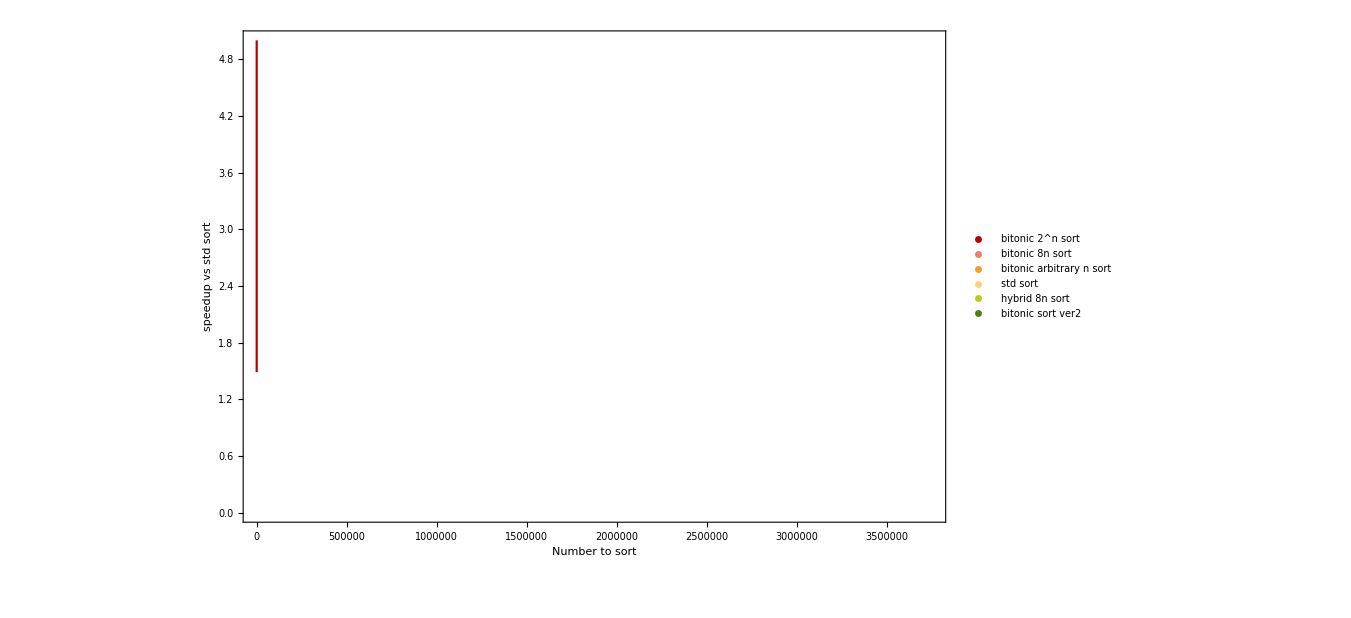

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{Automatic,{0,5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

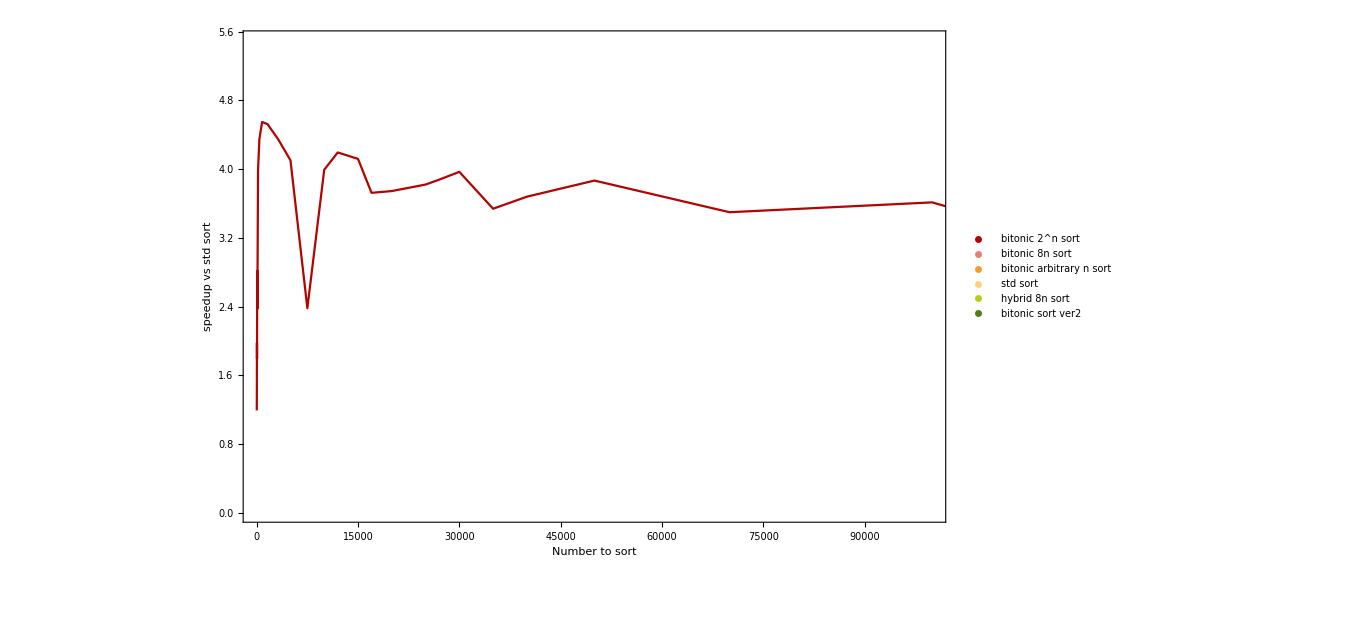

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0,100000},{0,5.5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```